## Mathematica Gnuplot Integration

### Basic examples

The gnuPlot function works (to some extend) analogous to the Mathematica Plot function.
The default plot variable is x and the default interval is from -5 to +5.

```mathematica
gnuPlot[0.05x^4-x^2]
```

-Graphics-

User defined variables and intervals can be given as second argument.
The option PlotStyle is used to add additional gnuplot commands before the automatically generated plot command.

```mathematica
gnuPlot[Exp[-y^2]Cos[2y],{y,-3,3},PlotStyle->"set grid y @DGRAY"]
```

-Graphics-

A set of functions can be given as first argument.
The third argument of gnuPlot is used to overwrite the default plot command.
The labels #1, #2, .. are used to identify the different data sets / functions. They are replaced internally by the respective file names.

```mathematica
gnuPlot[{-1/x,-1/x^3,0},{x,-5,5},"set xrange [-5:5]; set yrange [-2:2]; plot #1 @BLUE w l not, #2 @RED w l not, #3 @DGRAY w l not"]
```

-Graphics-

### Latex terminal

The cairolatex terminal can be used to set labels with Latex. Special characters have to be escaped.
The PlotSize option is used to modify the gnuplot output size.

```mathematica
gnuPlot[{Cos[x]^2 Exp[-x/2],BesselJ[2,x],0.3+0.1*Cos[x^2]/(1+x)},{x,0.01,4π},"set xtics 0,2,12; plot #1 @BLUE t '$\\cos(x^2)\\, e^{-x/2}$' w l, #2 @GREEN t '$J_2(x)$' w l, #3 w l @MAGENTA not",Latex->True,PlotSize->"6,4"]
```

-Graphics-

The LatexStyle option can be used to supply additional Tex commands. This can be used to change the font family, for example.

```mathematica
gnuPlot[{Exp[-x^2/2]Cos[10x]},{x,-3,5},"set ytics 0.5; set label '$\\psi_{1}(x)$' at 3.5, 0.2; plot #1 @TURQUOISE w l not",Latex->True,LatexStyle->"\\usepackage{cmbright}",PlotSize->"7,3"]
```

-Graphics-

### List plots

List plots work in the same way as the Mathematica ListPlot function.
Here, gnuplots boxes option is used to create a bar plot.

```mathematica
data=Table[Table[{k,PDF[PoissonDistribution[λ],k]},{k,0,35}],{λ,{10,20}}];
gnuListPlot[data,"set label '$k$' at graph 1.03, graph 0.02; plot [0:35] #1 @BLUE w boxes t '$P_{10}(k)$', #2 @RED w boxes t '$P_{20}(k)$'",PlotSize->"6,4",Latex->True]
```

-Graphics-

### Combined Data + Analytical plots

The gnuData helper function can be used to quicky create datasets from any analytic function.
Internally, the function gnuPlot uses gnuListPlot in combination with gnuData.

```mathematica
gnuListPlot[data~Join~gnuData[Exp[k(1+Log[10/k])-10]/Sqrt[2π(k+1/6)],{k,0.01,35},100],"plot #3 @RED w l not, #1 w p pt 4 lw 1 lc rgb '#000000' not",PlotSize->"8,3"]
```

-Graphics-

### Using gnuplots ‘multiplot’ feature

Not a feature of the script, but an easy way to use gnuplots extended features.

```mathematica
gnuListPlot[data,"set yrange[0:0.14]; set multiplot layout 1,2; plot [0:35] #1 @BLUE w boxes t 'P_{10}(k)'; plot [0:35] #2 @RED w boxes t 'P_{20}(k)'",PlotSize->"8,2.5",LineWidth->2]
```

-Graphics-

### Combining with Mathematica Graphics functions

The graphs are usual Mathematica Graphics objects and can be manipulated

```mathematica
g=gnuPlot[Cos[3x]Exp[-x^2/10],{x,-2π,2π},PlotStyle->"unset xtics; unset ytics; unset border",PlotSize->"2.2,2"];
Show[Graphics[Rotate[{Thick,{Lighter[Red],g[[1,2,1,1]]},{Lighter[Blue],Circle[{56.5,56},56]}},π/4]],ImageSize->100]
```

-Graphics-

### The PNG Terminal

PNG output works in the same way as PDF / Latex, but the size / linewidth and font options should be modified

```mathematica
gnuPlot[{Exp[-x^2/2]Cos[10x]},{x,-3,5},"set ytics 0.5; plot #1 w l @ORANGE not",PNG->True,PlotSize->"400,200",LineWidth->1,Font->"Verdana,11"]
```

-Graphics-

#### 3D plots

The gnuListPlot command can be used to create 3D plots as well.

```mathematica
f3d[x_,y_]:=Sin[1.3x]Cos[.9y]+Cos[.8x]Sin[1.9y]+Cos[.2x*y]
data3d=Flatten[Table[{x,y,f3d[x,y]}//N,{x,-5,5,0.05},{y,-5,5,0.05}],1];
gnuListPlot[{data3d},"@MATLAB; set pm3d map; set xrange [-5:5]; set yrange [-5:5]; splot #1 w pm3d not", PNG->True,PlotSize->"400,400",LineWidth->1,Font->"Verdana,11"]
```

-Graphics-

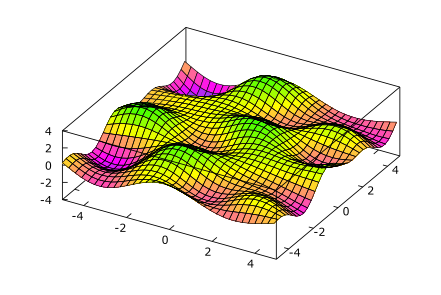

```mathematica
data3dcoarse=Flatten[Table[{x,y,f3d[x,y]}//N,{x,-5,5,0.3},{y,-5,5,0.3}],1];
gnuListPlot[{data3dcoarse},"@VIOLETGREEN; unset colorbox; set pm3d implicit at s hidden3d 100; unset hidden3d; unset surface; set ticslevel 0; set xrange [-5:5]; set yrange [-5:5]; set style line 100 lc rgb '#000000' lw 0.6 lt 1; set ztics 2; set border 4095 front linetype -1 lw 0.8; set view 30; splot #1 not",PlotSize->"8,5"]
```